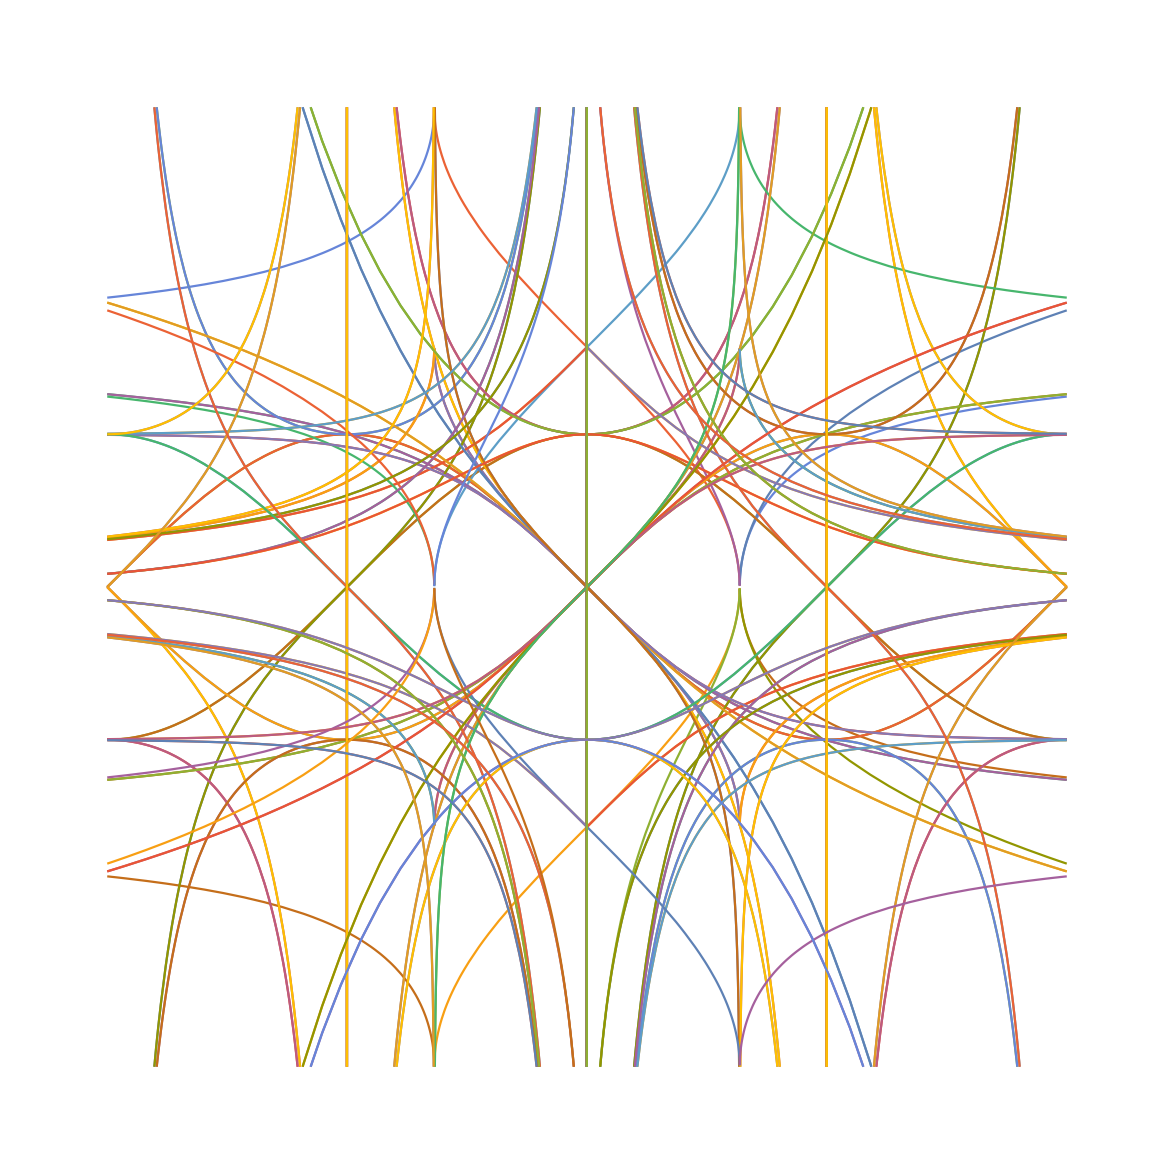

```mathematica
(*
	A plot of all the trig functions and inverse trig functions, reflected across both the x axis and the y axis. Currently hanging on the wall of my room!
*)
Plot[{Sin[x],ArcSin[x],Cos[x],ArcCos[x],Tan[x],ArcTan[x],Cot[x],ArcCot[x],Csc[x],ArcCsc[x],Sec[x],ArcSec[x],Sinh[x],ArcSinh[x],Cosh[x],ArcCosh[x],Tanh[x],ArcTanh[x],Coth[x],ArcCoth[x],Csch[x],ArcCsch[x],Sech[x],ArcSech[x],-Sin[x],-ArcSin[x],-Cos[x],-ArcCos[x],-Tan[x],-ArcTan[x],-Cot[x],-ArcCot[x],-Csc[x],-ArcCsc[x],-Sec[x],-ArcSec[x],-Sinh[x],-ArcSinh[x],-Cosh[x],-ArcCosh[x],-Tanh[x],-ArcTanh[x],-Coth[x],-ArcCoth[x],-Csch[x],-ArcCsch[x],-Sech[x],-ArcSech[x],Sin[-x],ArcSin[-x],Cos[-x],ArcCos[-x],Tan[-x],ArcTan[-x],Cot[-x],ArcCot[-x],Csc[-x],ArcCsc[-x],Sec[-x],ArcSec[-x],Sinh[-x],ArcSinh[-x],Cosh[-x],ArcCosh[-x],Tanh[-x],ArcTanh[-x],Coth[-x],ArcCoth[-x],Csch[-x],ArcCsch[-x],Sech[-x],ArcSech[-x],-Sin[-x],-ArcSin[-x],-Cos[-x],-ArcCos[-x],-Tan[-x],-ArcTan[-x],-Cot[-x],-ArcCot[-x],-Csc[-x],-ArcCsc[-x],-Sec[-x],-ArcSec[-x],-Sinh[-x],-ArcSinh[-x],-Cosh[-x],-ArcCosh[-x],-Tanh[-x],-ArcTanh[-x],-Coth[-x],-ArcCoth[-x],-Csch[-x],-ArcCsch[-x],-Sech[-x],-ArcSech[-x]},{x,-Pi,Pi},PlotRange->{-Pi,Pi},AspectRatio->1,Axes->False]
```

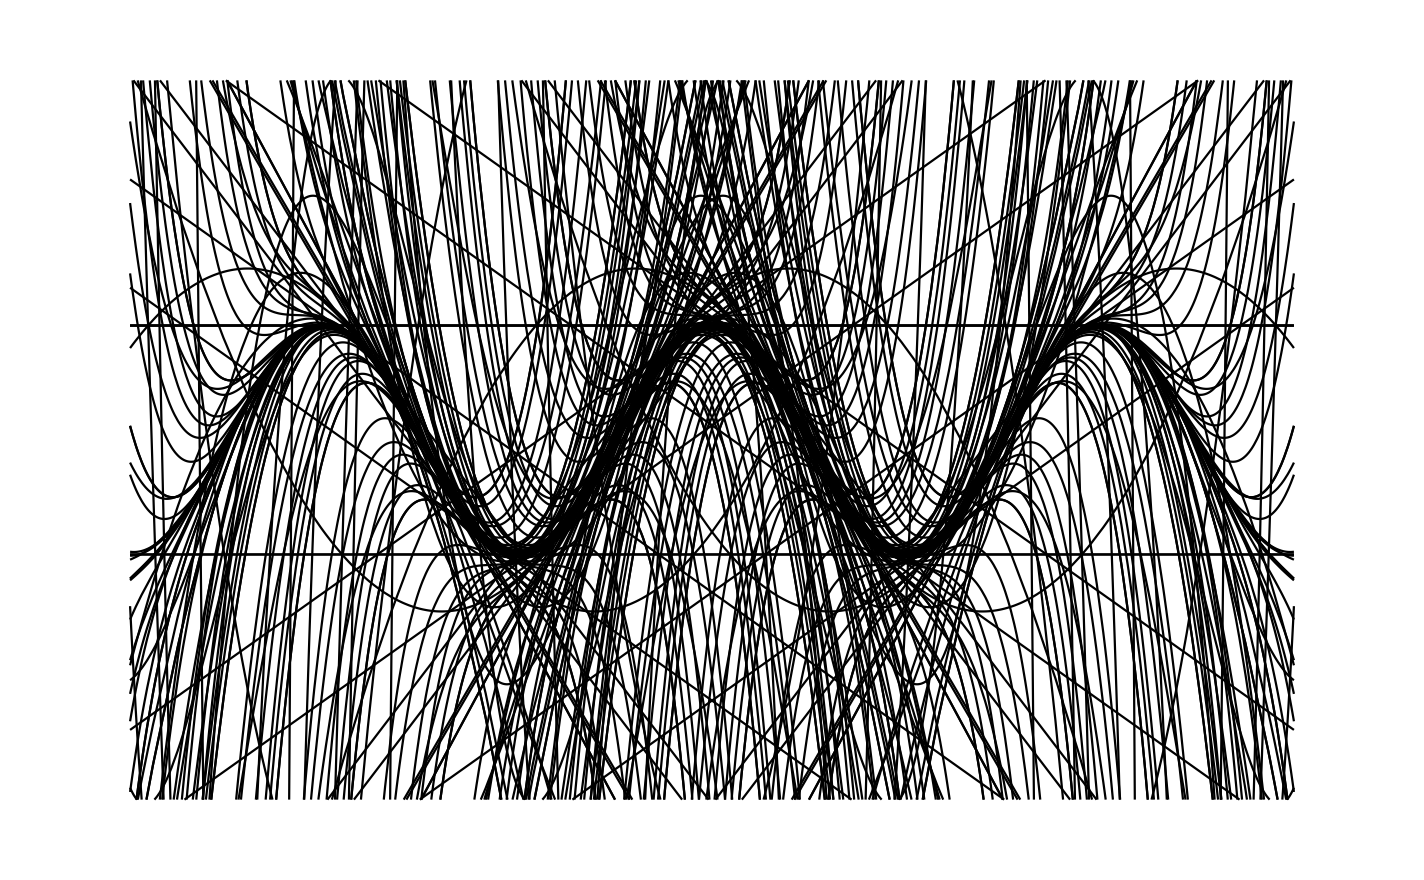

```mathematica
(*
	A plot of Taylor polynomials of Cos[x] of degree 1-8 centered at every Pi/8. Cos[x] is not plotted here but you can clearly see it appear.
*)
Plot[Evaluate@Flatten[Table[Table[Normal[Series[Cos[x],{x,xo,k}]],{k,1,8}],{xo,-2*Pi,2*Pi,Pi/8}]],{x,-3*Pi,3*Pi},PlotRange->{-Pi,Pi},PlotStyle->Black,Axes->False]
```

```mathematica
(*
	A dynamic plot of degree 1-8 taylor polynomials of Cos[x], centered at the position of your choice. Very nice!
*)
Manipulate[Plot[{Evaluate@Table[Normal[Series[Cos[x*1.],{x,mmm,k}]],{k,1,8}],Cos[x]},{x,-3*Pi,3*Pi},PlotRange->{-Pi,Pi}],{mmm,-2*Pi,2*Pi}]
```

```mathematica
(*
	A plot of the taylor polynomial of order 3 of Cos[x], centered at a point of your choice.
*)
Manipulate[Plot[{Normal[Series[Cos[x],{x,mmm,3}]]/.x->y,Cos[y]},{y,-3*Pi,3*Pi},PlotRange->{-Pi,Pi}],{mmm,-3*Pi,3*Pi}]
```